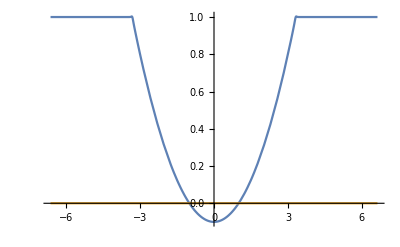

```mathematica
(*Configuration*)
a=0.1;
v=0.0000001;
n=100.;

b=(1.+1./a)^(-n);
Epsilon = Function[x,1.+(a*(x^2.-1.)+ⅈ*v-1.)/(1.+b*x^(2.n))];

X0=2.*Sqrt[1.+1./a];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

A=1.;
```

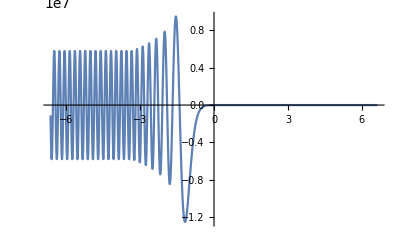

0.0000356109

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0.};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A};

ETE=ParametricNDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[ETE[0,30.][x]],{x,-X0,X0},PlotRange->Full]

RTE=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*ETE[θ,χ][-X0]-ETE[θ,χ]'[-X0])/(ⅈ*χ*ETE[θ,χ][-X0]+ETE[θ,χ]'[-X0])];
TTE=Function[{θ,χ},ETE[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTE[θ,χ]*Exp[-ⅈ*χ*(-X0)])/ETE[θ,χ][-X0]];

TEDissipation =Function[{θ,χ},1. - Abs[RTE[θ,χ]]^2.-Abs[TTE[θ,χ]]^2.];
TEDissipation[0.,30.]
```

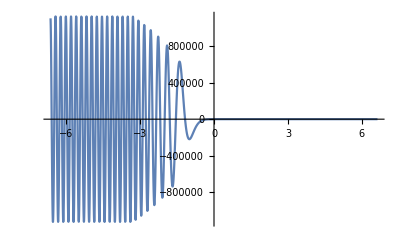

0.0000355848

```mathematica
(*TM-wave*)
BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0};
BTMInitials={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[θ]};

BTM=ParametricNDSolveValue[{BTMEquation,BTMInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[BTM[0.,30.][x]],{x,-X0,X0},PlotRange->Full]

RTM=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*BTM[θ,χ][-X0]-BTM[θ,χ]'[-X0])/(ⅈ*χ*BTM[θ,χ][-X0]+BTM[θ,χ]'[-X0])];
TTM=Function[{θ,χ},BTM[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTM[θ,χ]*Exp[-ⅈ*χ*(-X0)])/BTM[θ,χ][-X0]];

TMDissipation=Function[{θ,χ},1.-Abs[RTM[θ,χ]]^2.-Abs[TTM[θ,χ]]^2.];
TMDissipation[0.,30.]
```

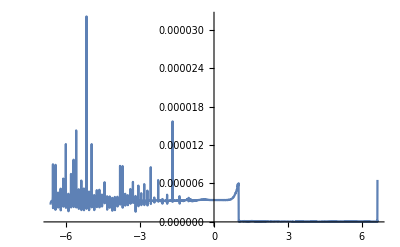

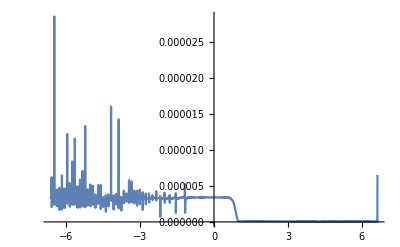

```mathematica
(*Reletive precision*)
values={θ->0.,χ->30.};
ETM=Function[x,ⅈ*BTM[θ,χ]'[x]/(χ*Epsilon[x])];
Plot[Abs[ETE[θ,χ][x]-ETM[x]]/Min[Abs[ETE[θ,χ][x]],Abs[ETM[x]]]/.values,{x,-X0,X0},PlotRange->Full]

BTE=Function[x,(-ⅈ/χ)*ETE[θ,χ]'[x]];
Plot[Abs[BTE[x]+BTM[θ,χ][x]]/Min[Abs[BTE[x]],Abs[BTM[θ,χ][x]]]/.values,{x,-X0,X0},PlotRange->Full]
```

```mathematica
limits={χ1->5.,χ2->30.};
Teta=Function[χ,Abs[θ/.Maximize[TMDissipation[θ,χ],θ][[2]]]];
Data=Table[Teta[x],{x,χ2}/.limits];
fit=FindFit[Data,x^m,m,x];
Experiment=ListPlot[Data];
Approximation=Plot[x^m/.fit,{x,χ1,χ2}/.limits];
Show[Experiment,Approximation,PlotLegends->Automatic]
```

NMaximize::nnum: The function value (ⅇ^Re[(0.`  - 13.2664991614216` ⅈ) x])^2.` Abs[-SuperscriptBox[TagBox[ParametricFunction[« 6 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][« 2 »],  is not a number at {θ} = {-0.829053}.

General::stop: Further output of NMaximize :: nnum will be suppressed during this calculation.

ReplaceAll::reps: {θ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindFit::nrlnum: The function value {1.  - 1.\ Abs[θ/. θ], 2.  - 1.\ Abs[θ/. θ]} is not a list of real numbers with dimensions {2} at {m} = {1.}.

Plot::pllim: Range specification {x, χ1, χ2}/. limits is not of the form {x, xmin, xmax}.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[], List[], List[]], List[Rule[DisplayFunction, Identity], Rule[PlotRangePadding, List[List[Scaled[0.02`], Scaled[0.02`]], List[Scaled[0.02`], Scaled[0.05`]]]], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0.`, 1], List[0, 1]]], Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 1], List[0, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[Scaled[0.02`], Scaled[0.02`]], List[Scaled[0.02`], Scaled[0.05`]]]], Rule[Ticks, List[Automatic, Automatic]]]], Plot[x^m/. fit, {x, χ1, χ2}/. limits], PlotLegends → Automatic.

Show[-Graphics-,Plot[x^m/.fit,{x,χ1,χ2}/.limits],PlotLegends→Automatic]